# Atome d'Hydrogène

## Initiation

Pour atome d' Hydrogène :

```mathematica
Z = 1;
```

```mathematica
n=4;l=1;m=0;
```

```mathematica
Clear[a]
```

## Équation de schrödinger

### La partie radiale de l'orbitale atomique

```mathematica
Subscript[R, n_,l_][r_]=√(((2Z)/(n a))^3 1/(2n)((n-l-1)!)/((n+l)!))  ((2Z r)/(n a))^l Subscript[L, n-l-1]^(2l+1)((2Z r)/(n a)) ⅇ^(-(Z r)/(n a))
```

((1/a^3)^(3/2) ⅇ^(-r/(4 a)) r (80 a^2-20 a r+r^2))/(256 √15)

```mathematica
Subscript[R, n,l][r]//Simplify
```

((1/a^3)^(3/2) ⅇ^(-r/(4 a)) r (80 a^2-20 a r+r^2))/(256 √15)

### La partie angulaire de l' orbitale atomique

```mathematica
Subscript[Y, l]^m(θ,ϕ)//Simplify
```

1/2 √(3/π) Cos[θ]

### La solution

```mathematica
Subscript[ψ, n_,l_,m_][r_,θ_,ϕ_]=Subscript[R, n,l][r]Subscript[Y, l]^m(θ,ϕ)
```

((1/a^3)^(3/2) ⅇ^(-r/(4 a)) r (80 a^2-20 a r+r^2) Cos[θ])/(512 √(5 π))

Rayon de Bohr :

```mathematica
a=1;
```

### La solution en coordonnées cartésiennes

```mathematica
Subscript[ψc, n_,l_,m_][x_,y_,z_]=Subscript[R, n,l][Sqrt[x^2+y^2+z^2]]Subscript[Y, l]^m(ArcCos[z/Sqrt[x^2+y^2+z^2]],ArcTan[x/y]);
```

## Demonstrations

```mathematica
Subscript[r, 0]=6;
Subscript[r, max]=50;
```

```mathematica
G1=Plot[r^2 (Subscript[R, n,l][r])^2,{r,0,Subscript[r, max]},Filling->Axis,AxesLabel->{r},PlotLabel->"Densité de probabilité radiale", PlotRange -> All];
```

```mathematica
G2=SphericalPlot3D[Abs[Subscript[ψ, n,l,m][Subscript[r, 0],θ,ϕ]],{θ,0,Pi},{ϕ,0,2Pi},Mesh->False,Boxed->False,Axes->None,PlotLabel->Style[With[{n=n,l=l,m=m},HoldForm[Abs[Subscript[ψ, n,l,m][Subscript[r, 0],θ,ϕ]]]],15],ColorFunction->"SunsetColors"];
```

```mathematica
G3=DensityPlot[Abs[Subscript[ψc, n,l,m][x,10^-30,z]],{x,-30,30},{z,-30,30},PlotPoints->100,Mesh->False,Frame->False,ColorFunction->"SunsetColors"];
```

```mathematica
GraphicsRow[{G1,G2,G3}]
```

-Graphics-

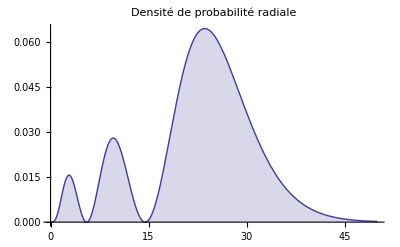

```mathematica
Plot[r^2 (Subscript[R, n,l][r])^2,{r,0,Subscript[r, max]},Filling->Axis,AxesLabel->{r},PlotLabel->"Densité de probabilité radiale", PlotRange -> All]
```

```mathematica
∫_0^∞ r^2 (Subscript[R, n,l][r])^2 ⅆr
```

1